Dataset[<>]

{2,2,2,2,2,2,2,3,3,3,5,5,5,5,5,5,5,6,7,7,7,7,7,7,7,7,7}

27

{λ1,λ2,λ3,λ4,λ5,λ6,λ7}

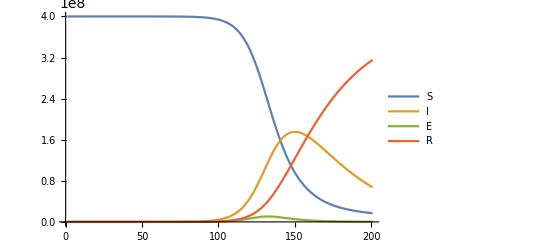

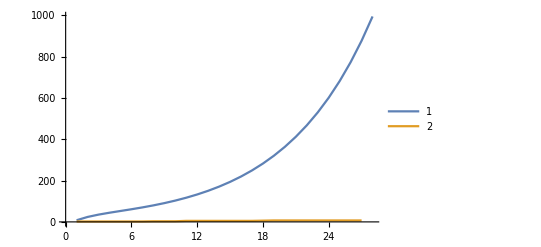

1.15081×10^6

RandomReal::precw: 参数 {-0.5,0.5} 的精度少于 WorkingPrecision (4.).

General::stop: 在本次计算中，RandomReal::precw 的进一步输出将被抑制.

{51.6,{x→0.6893,y→0.06413,m→0.6963,n→0.004584,z→0.115,p→1.249,q→0.3634}}

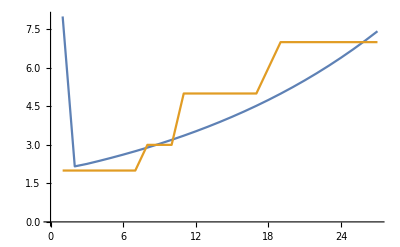

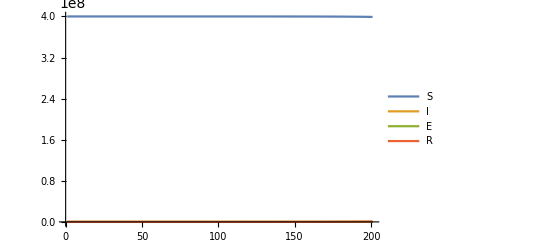

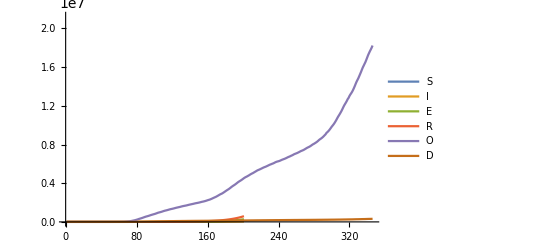

{{201,2}}

41281.8

153 days

```mathematica
db=ResourceFunction["COVIDTrackingData"]["USDaily"]
SOURCEDATA=Take[db[[All,{3,14}]],{-41,-15}][[All,1]]//Normal//Reverse
%//Length
DATA2=(db[[All,{3,14}]][All,#]//Normal//Reverse)&/@{"Positive","Death"};
DATA2=DATA2//.{Missing[]->0};
parameter=Table[ToExpression["λ"<>ToString[i]],{i,7}]
RuleList[a_]:=Thread[Rule[parameter,a]];
PrototypeModel[a_]:={-λ1 (#[[2]]*#[[1]])/Total@#-λ2 (#[[3]]*#[[1]])/Total@#+#[[1]],λ1 (1-λ6) (#[[2]]*#[[1]])/Total@#+λ2 λ7 (#[[3]]*#[[1]])/Total@#+λ3 #[[3]]-λ4 #[[2]]+#[[2]]+.0,λ2 (1-λ7) (#[[3]]*#[[1]])/Total@#+λ1 λ6 (#[[2]]*#[[1]])/Total@#-λ3 #[[3]]-λ5 #[[3]]+#[[3]]+.0,λ4 #[[2]]+λ5 #[[3]]+#[[4]]+.0}//.RuleList[a]&;
model=PrototypeModel[{0.1,0.5,0.8,0.03,0.01,0.8,0}];
Data=NestList[model,{4 10^8,8.,8.,0},200];
ListLinePlot[%//Transpose,PlotLegends->Characters["SIER"]]
Data;
ModelNestFunction[a_,b_,Nmax_]:=NestList[PrototypeModel[a],b,Nmax]
ModelNestFunction[{0.1,0.5,0.8,0.03,0.01,0.8,0},{4. 10^8,8.,20.,0},27][[All,2]];
ListLinePlot[{%,SOURCEDATA},PlotLegends->{1,2,3,4}]
Function1[x_Real,y_Real,z_Real,m_Real,n_Real,p_Real,q_Real]:=Module[{DATA},DATA=ModelNestFunction[{x,y,z,m,n,p,q},{4. 10^8,8.,10,0},26];
Return[(DATA[[All,2]]-SOURCEDATA)^2//Total]];
(*调试*)
Function1[0.1,0.5,0.8,0.03,0.01,0.8,0.]
(*拟合*)
Dynamic@x
ans=NMinimize[{Function1[x,y,z,m,n,p,q],1.>x>0,1>y>0,1.>z>0,(*1.>*)m>0,(*1.>*)p>0,1.>n>0,1.>q>0.},{{x,0.,1.},{y,0.,1.},{m,0.,1.},{n,0.,1.},{z,0.,1.},{p,0.,1.},{q,0.,1.}},Method->"SimulatedAnnealing",WorkingPrecision->4]
FITDATA=ModelNestFunction[{x,y,z,m,n,p,q}/.Last@ans,{4. 10^8,8.,8.,0},200];
FITDATA[[1;;27,2]];
ListLinePlot[{%,SOURCEDATA}]
ListPlot[FITDATA//Transpose,Joined->True,PlotLegends->Characters["SIEROD"]]
ListLinePlot[Join[FITDATA//Transpose,DATA2],PlotLegends->Characters["SIEROD"]]
Position[FITDATA,Max[FITDATA[[All,2]]]]
Max[FITDATA[[All,2]]]
DateObject["2020/7/29"]-DateObject@"2020/2/27"
```